## Wielomiany Hermite’a

```mathematica
$Assumptions = {L∈PositiveReals,ℏ ∈ PositiveReals, ω ∈ PositiveReals, m ∈ PositiveReals} ;
ℋ=-ℏ^2/(2m) Laplacian[u[x,y],{x,y}]+1/2 m ω^2 (x^2+y^2) u[x,y];
ℬ=DirichletCondition[u[x,y]==0,True];
{vals,funs}=DEigensystem[{ℋ,ℬ},u[x,y],{x,y}∈FullRegion[2],8];
vals[[1]]
```

(ω ℏ)/2

```mathematica
Norma=Table[Sqrt[Integrate[funs[[i]]^2,{x,y}∈Region[FullRegion[2]]]],{i,1,8}];
```

```mathematica
LKwant=Table[{0,0,k1,-k1},{k1,0,3}]
```

{{0,0,0,0},{0,0,1,-1},{0,0,2,-2},{0,0,3,-3}}

```mathematica
listProduct[x_List]:=Times@@x;
n= Table[Count[{LKwant[[i,3]],LKwant[[i,4]]}, j],{i,1,3},{j,-2,2}];
ns[i_]:=listProduct[Factorial[n[[i]]]];
```

```mathematica
vals= vals+ℏ ω/2;
```

```mathematica
funsz[i_,k_]:=1/Sqrt[L] 1/Norma[[i]] funs[[i]]*Exp[ⅈ k 2π z/L];
funsc[i_,k_]:=1/Sqrt[L] 1/Norma[[i]] funs[[i]]*Exp[-ⅈ k 2π z/L];
funse[i_,k_]:=1/Sqrt[L] 1/Norma[[i]](vals[[i]]+ℏ^2/(2m)(4 π^2 k^2)/L^2)*funs[[i]]*Exp[ⅈ k 2π z/L];

Ψ[a_,b_, k1_,k2_]=1/Sqrt[2]((funsz[a,k1]/.{x->x1,y->y1,z->z1})*(funsz[b,k2]/.{x->x2,y->y2,z->z2})+(funsz[b,k2]/.{x->x1,y->y1,z->z1})*(funsz[a,k1]/.{x->x2,y->y2,z->z2}));

Ψc[a_,b_, k1_,k2_]=1/Sqrt[2]((funsc[a,k1]/.{x->x1,y->y1,z->z1})*(funsc[b,k2]/.{x->x2,y->y2,z->z2})+(funsc[b,k2]/.{x->x1,y->y1,z->z1})*(funsc[a,k1]/.{x->x2,y->y2,z->z2}));

H[ x1_,y1_,x2_,y2_,z1_,z2_]=(-Laplacian[#,{x1,y1,z1,x2,y2,z2}]+2 (x1^2+y1^2+x2^2+y2^2)#)&;
Ψe[a_,b_, k1_,k2_]=1/Sqrt[2](vals[[a]]+vals[[b]]+ℏ^2/(2m)(4 π^2 k1^2)/L^2+ℏ^2/(2m)(4 π^2 k2^2)/L^2)*((funsz[a,k1]/.{x->x1,y->y1,z->z1})*(funsz[b,k2]/.{x->x2,y->y2,z->z2})+(funsz[b,k2]/.{x->x1,y->y1,z->z1})*(funsz[a,k1]/.{x->x2,y->y2,z->z2}));

Ψc[1,1,1,-1]Ψe[1,1,1,-1]
```

Part::pkspec1: The expression a cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression a cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression a cannot be used as a part specification.

Part::pkspec1: The expression b cannot be used as a part specification.

Part::pkspec1: The expression a cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

1/2 (2 ω ℏ+(4 π^2 ℏ^2)/(L^2 m)) ((ⅇ^((2 ⅈ π z1)/L-(2 ⅈ π z2)/L-(m x1^2 ω)/(2 ℏ)-(m x2^2 ω)/(2 ℏ)-(m y1^2 ω)/(2 ℏ)-(m y2^2 ω)/(2 ℏ)) √((m ω)/ℏ) √(m ω ℏ))/(L π ℏ)+(ⅇ^(-(2 ⅈ π z1)/L+(2 ⅈ π z2)/L-(m x1^2 ω)/(2 ℏ)-(m x2^2 ω)/(2 ℏ)-(m y1^2 ω)/(2 ℏ)-(m y2^2 ω)/(2 ℏ)) √((m ω)/ℏ) √(m ω ℏ))/(L π ℏ))^2

```mathematica
diagA = DiagonalMatrix[Table[1/ns[i] Integrate[Integrate [Ψc[1,1,LKwant[[i,3]],LKwant[[i,4]]]Ψe[1,1,LKwant[[i,3]],LKwant[[i,4]]], {x1,y1,x2,y2}∈Region[FullRegion[4]]],{z1,0,L},{z2,0,L}],{i,3}]];
diagM=MatrixForm[%]
```

((2 ω √(m ω ℏ))/(√((m ω)/ℏ)) | 0 | 0
0 | 2 ℏ (ω+(2 π^2 ℏ)/(L^2 m)) | 0
0 | 0 | 2 ℏ (ω+(8 π^2 ℏ)/(L^2 m)))

```mathematica
deltA = Table[Integrate[Integrate [1/Sqrt[ns[i]ns[j]] Ψc[1,1,LKwant[[i,3]],LKwant[[i,4]]]DiracDelta[(x1-x2),(y1-y2),(z1-z2)]Ψ[1,1,LKwant[[j,3]],LKwant[[j,4]]], {x1,y1,x2,y2}∈Region[FullRegion[4]]],{z1,-L,L},{z2,-L,L}],{i,3},{j,3}];
deltM = MatrixForm[%]
```

((m ω)/(L π ℏ) | (√2 m ω)/(L π ℏ) | (√2 m ω)/(L π ℏ)
(√2 m ω)/(L π ℏ) | (2 m ω)/(L π ℏ) | (2 m ω)/(L π ℏ)
(√2 m ω)/(L π ℏ) | (2 m ω)/(L π ℏ) | (2 m ω)/(L π ℏ))

```mathematica
jord =JordanDecomposition[diagA +g deltA];
MatrixForm[jord[[1]]]
MatrixForm[jord[[2]]]
```

((2 L^2 m ω ℏ+16 π^2 ℏ^2-L^2 m Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,1])/(√2 L^2 (2 √((m ω)/ℏ) ℏ √(m ω ℏ)-m Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,1])) | (2 L^2 m ω ℏ+16 π^2 ℏ^2-L^2 m Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,2])/(√2 L^2 (2 √((m ω)/ℏ) ℏ √(m ω ℏ)-m Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,2])) | (2 L^2 m ω ℏ+16 π^2 ℏ^2-L^2 m Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,3])/(√2 L^2 (2 √((m ω)/ℏ) ℏ √(m ω ℏ)-m Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,3]))
(-(2 g^2 m^2 ω^2)/(L^2 π^2 ℏ^2)+((g m ω)/(L π ℏ)+(2 ω √(m ω ℏ))/(√((m ω)/ℏ))-Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,1]) ((2 g m ω)/(L π ℏ)+(2 ℏ (L^2 m ω+8 π^2 ℏ))/(L^2 m)-Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,1]))/(-(4 g ω √((m ω)/ℏ) √(m ω ℏ))/(L π)+(2 g m ω Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,1])/(L π ℏ)) | (-(2 g^2 m^2 ω^2)/(L^2 π^2 ℏ^2)+((g m ω)/(L π ℏ)+(2 ω √(m ω ℏ))/(√((m ω)/ℏ))-Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,2]) ((2 g m ω)/(L π ℏ)+(2 ℏ (L^2 m ω+8 π^2 ℏ))/(L^2 m)-Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,2]))/(-(4 g ω √((m ω)/ℏ) √(m ω ℏ))/(L π)+(2 g m ω Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,2])/(L π ℏ)) | (-(2 g^2 m^2 ω^2)/(L^2 π^2 ℏ^2)+((g m ω)/(L π ℏ)+(2 ω √(m ω ℏ))/(√((m ω)/ℏ))-Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,3]) ((2 g m ω)/(L π ℏ)+(2 ℏ (L^2 m ω+8 π^2 ℏ))/(L^2 m)-Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,3]))/(-(4 g ω √((m ω)/ℏ) √(m ω ℏ))/(L π)+(2 g m ω Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,3])/(L π ℏ))
1 | 1 | 1)

(Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,1] | 0 | 0
0 | Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,2] | 0
0 | 0 | Root[-4 g L^4 m^3 ω^3 √((m ω)/ℏ) ℏ^2-40 g L^2 m^2 π^2 ω^2 √((m ω)/ℏ) ℏ^3-64 g m π^4 ω √((m ω)/ℏ) ℏ^4-16 g L^4 m^3 ω^3 ℏ √(m ω ℏ)-80 g L^2 m^2 π^2 ω^2 ℏ^2 √(m ω ℏ)-8 L^5 m^2 π ω^3 ℏ^3 √(m ω ℏ)-80 L^3 m π^3 ω^2 ℏ^4 √(m ω ℏ)-128 L π^5 ω ℏ^5 √(m ω ℏ)+(12 g L^4 m^3 ω^2 √((m ω)/ℏ) ℏ+60 g L^2 m^2 π^2 ω √((m ω)/ℏ) ℏ^2+4 L^5 m^2 π ω^2 √((m ω)/ℏ) ℏ^3+40 L^3 m π^3 ω √((m ω)/ℏ) ℏ^4+64 L π^5 √((m ω)/ℏ) ℏ^5+8 g L^4 m^3 ω^2 √(m ω ℏ)+8 L^5 m^2 π ω^2 ℏ^2 √(m ω ℏ)+40 L^3 m π^3 ω ℏ^3 √(m ω ℏ)) #1+(-5 g L^4 m^3 ω √((m ω)/ℏ)-4 L^5 m^2 π ω √((m ω)/ℏ) ℏ^2-20 L^3 m π^3 √((m ω)/ℏ) ℏ^3-2 L^5 m^2 π ω ℏ √(m ω ℏ)) #1^2+L^5 m^2 π √((m ω)/ℏ) ℏ #1^3&,3])

```mathematica
En=Diagonal[jord[[2]]];
```

```mathematica
ℏ=1;
m=1;
ω=1;
```

```mathematica
list =Table[{g,Min[En/.{L->10}]},{g,0,1000,1}];
```

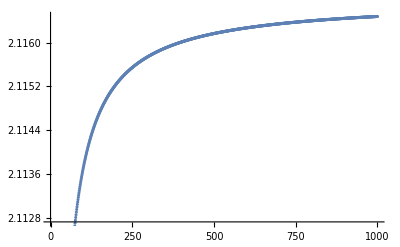

```mathematica
ListPlot[list]
```

```mathematica
Plot[]
```